```mathematica
ClearAll["Global`*"]
Get["RunDec`"]
nc=3;
nf=3;
Mz=91.1876;
orderbeta = 5;
const={nc ->3, nf->3}
AppendTo[const, cf->(nc^2-1)/2/nc /. const]
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

{3→3,3→3}

{3→3,3→3,cf→4/3}

## Beta

```mathematica
betarule:=Module[{beta={11/2-nf/3,51/4-19/12*nf,2857/64-5033/576*nf+325/1728*nf^2,149753/768+891/32*Zeta[3]-(1078361/20736+1627/864*Zeta[3])*nf+(50065/20736+809/1296*Zeta[3])*nf^2+1093/93312*nf^3,2/4^5*(8157455/16+621885/2*Zeta[3]-88209/2*Zeta[4]-288090*Zeta[5]+nf*(-336460813/1944-4811164/81*Zeta[3]+33935/6*Zeta[4]+1358995/27*Zeta[5])+nf^2*(25960913/1944+698531/81*Zeta[3]-10526/9*Zeta[4]-381760/81*Zeta[5])+nf^3*(-630559/5832-48722/243*Zeta[3]+1618/27*Zeta[4]+460/9*Zeta[5])+nf^4*(1205/2916-152/81*Zeta[3]))}},Join[Table[b[n]->beta[[n]],{n,1,Length[beta]}],Table[b[n]->0,{n,Length[beta]+1,orderbeta}]]]
```

## Gamma

### Gamma 1

```mathematica
g1 = N[3/2 Cf[Nc], 18]
```

1.5 Cf(Nc)

### Gamma 2

```mathematica
g2 =N[Cf[Nc]/48(97Nc+9 Cf[Nc]-10 Nf),18]
```

0.0208333333333333333 Cf(Nc) (9. Cf(Nc)+97. Nc-10. Nf)

### Gamma 3

```mathematica
g3=N[Cf[Nc]/32( 11413/108 Nc^2 - 129/4 Nc Cf[Nc] -(278/27+24 Zeta[3])Nc Nf + 129/2 Cf[Nc]^2 - (23-24 Zeta[3]) Cf[Nc] Nf - 35/27 Nf^2), 18]
```

0.03125 Cf(Nc) (5.84936567583026285 Nf Cf(Nc)-32.25 Nc Cf(Nc)+64.5 (Cf(Nc))^2+105.675925925925926 Nc^2-39.1456619721265591 Nc Nf-1.2962962962962963 Nf^2)

## Adler-Function c(n,k)

```mathematica
cRule1 :=Module[ {adlerC={{1},
 {365/24-11*Zeta[3]-(11/12-2/3*Zeta[3])*nf},
{87029/288-1103/4*Zeta[3]+275/6*Zeta[5]-(7847/216-262/9*Zeta[3]+25/9*Zeta[5])*nf +(151/162-19/27*Zeta[3])*nf^2},
{78631453/20736-1704247/432*Zeta[3]+4185/8*Zeta[3]^2+34165/96*Zeta[5]-1995/16*Zeta[7]}
}},Table[Do[Return[c[n][k]->adlerC[[n]][[k]]],{k,1}],{n,1,Length[adlerC]}]]

cRule2 :=Module[ {adlerC={{1,0, 0, 0, 0},
 {365/24-11*Zeta[3]-(11/12-2/3*Zeta[3])*nf,-1/4*b[1]*c[1][1], 0, 0, 0},
{87029/288-1103/4*Zeta[3]+275/6*Zeta[5]-(7847/216-262/9*Zeta[3]+25/9*Zeta[5])*nf +(151/162-19/27*Zeta[3])*nf^2, 1/4(-b[2]*c[1][1]-2*b[1]*c[2][1]), 1/12*b[1]^2*c[1][1],0 ,0},
{78631453/20736-1704247/432*Zeta[3]+4185/8*Zeta[3]^2+34165/96*Zeta[5]-1995/16*Zeta[7], 1/4*(-b[3]*c[1][1]-2*b[2]*c[2][1]-3*b[1]*c[3][1]), 1/24*(6*c[2][1]*b[1]^2+5*b[2]*b[1]*c[1][1]), -1/32*b[1]^3*c[1][1],0},
{51, 1/4*(-b[4]*c[1][1]-2*b[3]*c[2][1]-3*b[2]*c[3][1]-4*b[1]*c[4][1]), 1/24*(12*c[3][1]*b[1]^2+6*b[1]*b[3]*c[1][1]+14*b[2]*b[1]*c[2][1]+3*b[2]^2*c[1][1]), 1/96*(-12*b[1]^3*c[2][1]-13*b[2]*b[1]^2*c[1][1]), 1/80*b[1]^4*c[1][1]}
}/.cRule1/.betarule},Table[c[n][k]->adlerC[[n]][[k]],{k,1,5}, {n,1,Length[adlerC]}]]
cRule :=Join[cRule2[[1]], cRule2[[2]], cRule2[[3]],cRule2[[4]], cRule2[[5]], {c[0][1]-> 1}]
```

```mathematica
Do[Print["c[",i,"][",j,"] =",N[c[i][j]/.cRule,15]],{i,1,5},{j,1,5}]
```

c[1][1] =1.

c[1][2] =0

c[1][3] =0

c[1][4] =0

c[1][5] =0

c[2][1] =1.63982120489698

c[2][2] =-1.125

c[2][3] =0

c[2][4] =0

c[2][5] =0

c[3][1] =6.37101448310094

c[3][2] =-5.68959771101822

c[3][3] =1.6875

c[3][4] =0

c[3][5] =0

c[4][1] =49.075700002948

c[4][2] =-33.0914066167203

c[4][3] =15.801594849791

c[4][4] =-2.84765625

c[4][5] =0

c[5][1] =51.

c[5][2] =-299.177187205152

c[5][3] =129.577532569234

c[5][4] =-40.6160884120297

c[5][5] =5.12578125

## Adler Function

```mathematica
L[s_]:=Log[-s/(Mz)^2]
α= AlphasExact[asMz/.NumDef, Mz/.NumDef,1, Mz/.NumDef,3]
α=0.1181;
```

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`26.`).

0.021461086527985190693

```mathematica
D0SecondOrder[s_] := nc/(12*Pi^2)*(c[0][1]+c[1][1]*α*(c[2][1]-1/2*b[1]*c[1][1]*L[s])*α^2)/.cRule/.betarule
```

```mathematica
D0SecondOrder[-0.1]//N
```

0.0253296

```mathematica
α
```

0.1181

```mathematica
D0[s_]:=nc/(12*Pi^2)*Sum[α^n*Sum[k*c[n][k]*L[s]^(k-1),{k,1,n+1}],{n,0,4}]/.betarule/.cRule
```

```mathematica
N[Integrate[D0[2.5*Exp[I x]], {x, 0, 2Pi}],15]
```

0.600566

```mathematica
N[D0[1*Exp[I*(1+I)]],15]
```

0.136903+0.0582164 ⅈ

```mathematica
N[D0[-10],15]
```

0.0773029

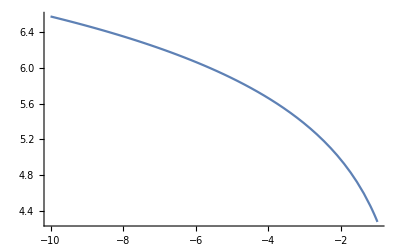

```mathematica
Plot[L[s], {s, -10, -1}]
```

```mathematica
nc/Pi^2/12//N
```

0.0253303

```mathematica
c[0][1]/.cRule
```

1

```mathematica
L[-2.]^0
```

1.

```mathematica
c[1][1]/.cRule
```

1

```mathematica
c[1][2]/.cRule
```

0

```mathematica
Integrate[1/2/Pi/I Exp[I w +2]/(w-I epsilon), {w, -Infinity, Infinity}]
```

ConditionalExpression[1/(4 π epsilon)ⅇ^2 (-2 -√(-epsilon^2) sgn(Im(log(-ⅈ/epsilon))) (√(-epsilon^2) sinh(epsilon sgn(Im(log(-ⅈ/epsilon))))+ⅈ epsilon cosh(epsilon sgn(Im(log(-ⅈ/epsilon)))))+-√(-epsilon^2) sgn(Im(log(ⅈ/epsilon))) (2 ⅈ epsilon cosh(epsilon sgn(Im(log(ⅈ/epsilon))))-2 √(-epsilon^2) sinh(epsilon sgn(Im(log(ⅈ/epsilon)))))+2 epsilon sgn(Im(log(-ⅈ/epsilon))) (√(-epsilon^2) cosh(epsilon sgn(Im(log(-ⅈ/epsilon))))+ⅈ epsilon sinh(epsilon sgn(Im(log(-ⅈ/epsilon)))))+2 epsilon sgn(Im(log(ⅈ/epsilon))) (√(-epsilon^2) cosh(epsilon sgn(Im(log(ⅈ/epsilon))))-ⅈ epsilon sinh(epsilon sgn(Im(log(ⅈ/epsilon)))))+π (epsilon cosh(epsilon sgn(Im(log(-ⅈ/epsilon))))-ⅈ √(-epsilon^2) sinh(epsilon sgn(Im(log(-ⅈ/epsilon)))))+π (ⅈ √(-epsilon^2) sinh(epsilon sgn(Im(log(ⅈ/epsilon))))+epsilon cosh(epsilon sgn(Im(log(ⅈ/epsilon)))))),Re(epsilon)≠0]

```mathematica
D[Exp[I t],t]
```

ⅈ ⅇ^(ⅈ t)

```mathematica
D[Cos[x]+I Sin[x],x]
```

-sin(x)+ⅈ cos(x)